```mathematica
Nx=15;
Ny=15;
nx=15;
ny=15;

datrotuwsoca=Flatten[Import["trot_0.4_nutcalca.dat"]];
datrotdwsoca=Flatten[Import["trot_0.4_ndtcalca.dat"]];
datrotuwsocb=Flatten[Import["trot_0.4_nutcalcb.dat"]];
datrotdwsocb=Flatten[Import["trot_0.4_ndtcalcb.dat"]];
```

```mathematica
impdiffdata=Table[Partition[(datrotuwsoca+datrotdwsoca),3][[i,1]] + Partition[(datrotuwsoca+datrotdwsoca),3][[i,2]]+ Partition[(datrotuwsoca+datrotdwsoca),3][[i,3]],{i,1,Nx*Ny}];

diffdata=impdiffdata;
```

```mathematica
impdiffdatb=Table[Partition[(datrotuwsocb+datrotdwsocb),3][[i,1]] + Partition[(datrotuwsocb+datrotdwsocb),3][[i,2]]+ Partition[(datrotuwsocb+datrotdwsocb),3][[i,3]],{i,1,Nx*Ny}];

diffdatb=impdiffdatb;
```

```mathematica
plotdiffdata=Partition[Riffle[diffdata,Table[0,{i,Length[diffdata]}]],2*Sqrt[Length[diffdata]]];
plotdiffdatb=Partition[Riffle[Table[0,{i,Length[diffdatb]}],diffdatb],2*Sqrt[Length[diffdatb]]];
plotdiffdatab=Riffle[plotdiffdata,plotdiffdatb];
```

```mathematica
length=Sqrt[Length[diffdata]];
hlength=IntegerPart[length/2];
```

```mathematica
l=0;
For[i=1,i<=nx,i++,
For[j=1,j<=ny,j++,
xpos=(j-1) - (i - 1);
ypos=(j-1) + (i - 1);
l = l+1;
coorda[l] = {xpos,ypos};
];];
l=0;
For[i=1,i<=nx,i++,
For[j=1,j<=ny,j++,
xpos=(j-1) - (i - 1);
ypos=(j-1) + (i - 1)+1;
l = l+1;
coordb[l] = {xpos,ypos};
];];
rownumber=7;
countatom=7;

midatom=(nx*rownumber + countatom)+1;
midcoord=coorda[midatom];
```

```mathematica
For[l=1,l<=nx*ny,l++,
newcoorda[l] = coorda[l] - midcoord];
For[l=1,l<=nx*ny,l++,
newcoordb[l] = coordb[l] - midcoord];

ndiffdata = Table[Flatten[{newcoorda[l] ,diffdata[[l]],l}],{l,1,nx*ny}];
ndiffdatb = Table[Flatten[{newcoordb[l] ,diffdatb[[l]],nx*ny+l}],{l,1,nx*ny}];
```

```mathematica
alldiffdata= Join[ndiffdata ,ndiffdatb ];
limval = alldiffdata[[All,3]];
minval=3.96;
maxval=3.97;
```

```mathematica
squarelength=3;
xmax=squarelength;
xmin=-squarelength;
ymax=squarelength;
ymin=-squarelength;

posmidcoord = {0,0};
coordx1 = xmin;
coordy1 = ymin;
coordx2 = xmax;
coordy2 = ymin;
coordx3 = xmax;
coordy3 = ymax;
coordx4 = xmin;
coordy4 = ymax;

squareline=
{Blue,Thickness[0.01],Line[{{{coordx1,coordy1},{coordx2,coordy2}},{{coordx2,coordy2},{coordx3,coordy3}},{{coordx3,coordy3},{coordx4,coordy4}},{{coordx4,coordy4},{coordx1,coordy1}}}]};
```

```mathematica
rmvpoints1=DeleteCases[Table[If[alldiffdata[[i,1]]>coordx3,pt=Null,If[alldiffdata[[i,2]]>coordy3,pt=Null,pt={alldiffdata[[i,1]],alldiffdata[[i,2]],alldiffdata[[i,3]],alldiffdata[[i,4]]}]];pt,{i,1,Length[alldiffdata]}],Null];

rmvpoints2=DeleteCases[Table[If[rmvpoints1[[i,1]]<coordx1,pt=Null,If[rmvpoints1[[i,2]]<coordy1,pt=Null,pt={rmvpoints1[[i,1]],rmvpoints1[[i,2]],rmvpoints1[[i,3]],rmvpoints1[[i,4]]}]];pt,{i,1,Length[rmvpoints1]}],Null];
```

```mathematica
slimval=rmvpoints2[[All,3]];
sminval=Min[slimval];
smaxval=Max[slimval];
spointlegend=BarLegend[{"Rainbow",{sminval,smaxval}},LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,24]}];
```

```mathematica
crldosa=DeleteCases[Table[If[rmvpoints2[[l,4]]<=nx*ny,pt={rmvpoints2[[l,1]],rmvpoints2[[l,2]],rmvpoints2[[l,4]]},pt=Null];pt,{l,1,Length[rmvpoints2]}],Null];
ldosa=crldosa[[All,3]];

crldosb=DeleteCases[Table[If[rmvpoints2[[l,4]]>nx*ny,pt={rmvpoints2[[l,1]],rmvpoints2[[l,2]],rmvpoints2[[l,4]]},pt=Null];pt,{l,1,Length[rmvpoints2]}],Null];
ldosb=crldosb[[All,3]];
ivalldos=Join[Flatten[Table[(ldosa[[l]]-1)*3+n+nx*ny*3*2*s,{l,1,Length[ldosa]},{s,0,1},{n,1,3}]],
Flatten[Table[(ldosb[[l]]-1)*3+n+nx*ny*3*2*s,{l,1,Length[ldosb]},{s,0,1},{n,1,3}]]];
Export["ivalldos.dat",ivalldos];
ldosdat=Import["wmax3.5_Ny15_Nx15_eta0.12_Ns40_ldostotal.dat"];
plldosdat=Partition[ldosdat[[All,2]],6];
fnplldosdat=Table[Total[plldosdat[[i]]],{i,1,Length[plldosdat]}];
```

```mathematica
ldoscoorda = crldosa[[All,{1,2}]];
ldoscoordb = crldosb[[All,{1,2}]];
fnldoscoordwor=Join[ldoscoorda,ldoscoordb];
fnldoscoord=Table[RotationMatrix[90 Degree].fnldoscoordwor[[i]],{i,1,Length[fnldoscoordwor]}];

fnldoscoorddat=Table[If[-2<=fnldoscoord[[i,1]]<=2&&-2<=fnldoscoord[[i,2]]<=2,pt=fnldoscoord[[i]],pt={None,None}];pt,{i,1,Length[fnldoscoord]}];
```

```mathematica
finpldos=fnplldosdat[[DeleteCases[Table[If[NumericQ[fnldoscoorddat[[i,1]]],pt=i,pt=None];pt,{i,1,Length[fnplldosdat]}],None]]];
finpcoord=fnldoscoorddat[[DeleteCases[Table[If[NumericQ[fnldoscoorddat[[i,1]]],pt=i,pt=None];pt,{i,1,Length[fnplldosdat]}],None]]];
finldosplot=Table[Flatten[{finpcoord[[i]],finpldos[[i]]}],{i,1,Length[finpldos]}];
```

```mathematica
ldossquarelength=2;
ldosxmax=ldossquarelength;
ldosxmin=-ldossquarelength;
ldosymax=ldossquarelength;
ldosymin=-ldossquarelength;

ldosposmidcoord = {0,0};
ldoscoordx1 = ldosxmin;
ldoscoordy1 = ldosymin;
ldoscoordx2 = ldosxmax;
ldoscoordy2 = ldosymin;
ldoscoordx3 = ldosxmax;
ldoscoordy3 = ldosymax;
ldoscoordx4 = ldosxmin;
ldoscoordy4 = ldosymax;
```

```mathematica
slcoordx11=-2.5;
slcoordy11=1.5;
slcoordx12=-1.5;
slcoordy12=1.5;
slcoordx13=-1.5;
slcoordy13=2.5;
slcoordx14=-2.5;
slcoordy14=2.5;
slsquareline1={Purple,Dashed,Thickness[0.015],Line[{{{slcoordx11,slcoordy11},{slcoordx12,slcoordy12}},{{slcoordx12,slcoordy12},{slcoordx13,slcoordy13}},{{slcoordx13,slcoordy13},{slcoordx14,slcoordy14}},{{slcoordx14,slcoordy14},{slcoordx11,slcoordy11}}}]};
```

```mathematica
slcoordx21=1.5;
slcoordy21=1.5;
slcoordx22=2.5;
slcoordy22=1.5;
slcoordx23=2.5;
slcoordy23=2.5;
slcoordx24=1.5;
slcoordy24=2.5;
slsquareline2={Purple,Dashed,Thickness[0.015],Line[{{{slcoordx21,slcoordy21},{slcoordx22,slcoordy22}},{{slcoordx22,slcoordy22},{slcoordx23,slcoordy23}},{{slcoordx23,slcoordy23},{slcoordx24,slcoordy24}},{{slcoordx24,slcoordy24},{slcoordx21,slcoordy21}}}]};
```

```mathematica
slcoordx31=-0.5;
slcoordy31=1.5;
slcoordx32=0.5;
slcoordy32=1.5;
slcoordx33=0.5;
slcoordy33=2.5;
slcoordx34=-0.5;
slcoordy34=2.5;
slsquareline3={Orange,Dashed,Thickness[0.015],Line[{{{slcoordx31,slcoordy31},{slcoordx32,slcoordy32}},{{slcoordx32,slcoordy32},{slcoordx33,slcoordy33}},{{slcoordx33,slcoordy33},{slcoordx34,slcoordy34}},{{slcoordx34,slcoordy34},{slcoordx31,slcoordy31}}}]};
```

```mathematica
slcoordx41=-2.5;
slcoordy41=-0.5;
slcoordx42=-1.5;
slcoordy42=-0.5;
slcoordx43=-1.5;
slcoordy43=0.5;
slcoordx44=-2.5;
slcoordy44=0.5;
slsquareline4={Orange,Dashed,Thickness[0.015],Line[{{{slcoordx41,slcoordy41},{slcoordx42,slcoordy42}},{{slcoordx42,slcoordy42},{slcoordx43,slcoordy43}},{{slcoordx43,slcoordy43},{slcoordx44,slcoordy44}},{{slcoordx44,slcoordy44},{slcoordx41,slcoordy41}}}]};
```

```mathematica
ldosminval=1.68;
fldosminval =1.68;
ldosmaxval=1.77;
fldosmaxval=1.77;
```

```mathematica
plfinldosplot=Table[
If[finldosplot[[i,3]]<=fldosminval,pt={finldosplot[[i,1]],finldosplot[[i,2]],fldosminval},If[finldosplot[[i,3]]>=fldosmaxval, pt = {finldosplot[[i,1]],finldosplot[[i,2]],fldosmaxval},pt={finldosplot[[i,1]],finldosplot[[i,2]],finldosplot[[i,3]]}]];pt,{i,1,Length[finldosplot]}];
```

```mathematica
rmvpoints2[[All,3]];
ccxcoord=finldosplot[[All,1]];
ccycoord=finldosplot[[All,2]];

chxcoord=-2;
chycoord=1;
sdelta=0.001;
For[i=1,i<=Length[finldosplot],i++,
If[chxcoord-sdelta<ccxcoord[[i]]&&ccxcoord[[i]]<chxcoord+sdelta&&chycoord-sdelta<ccycoord[[i]]&&ccycoord[[i]]<chycoord+sdelta,
point=finldosplot[[i]]]]
point;
```

```mathematica
colorscheme={{1.68,Purple},{1.69,Brown},{1.705,Red},{1.72,Cyan},{1.75,Gray}};

spointlegend=BarLegend[{(Blend[colorscheme,#]&),{fldosminval,fldosmaxval}},LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,24]}];
```

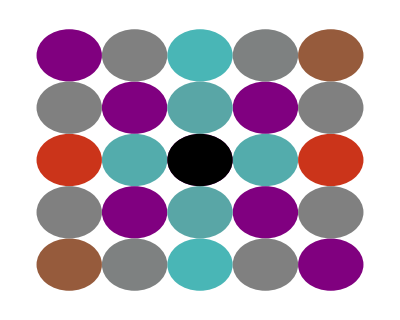

```mathematica
sqgraphicsldosplot = Graphics[Join[Table[{Blend[colorscheme,plfinldosplot[[i,3]]],Rotate[Disk[{finldosplot[[i,1]],finldosplot[[i,2]]},{0.5,0.5}],0]},{i,1,Length[plfinldosplot]}],{Black,Disk[{0,0},{0.5,0.5}]}],LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,24]},ImagePadding->{{5,5},{5,3}},ImageSize->400,AspectRatio->0.8];
ldosplot =sqgraphicsldosplot 
Export["ldosplot.eps",ldosplot];
Export["spointlodslegend.png",spointlegend];
```